# BE/CS 196a Lab 03 Protocol design and rate measurement of a DNA-strand-displacement reaction

## CRN Simulator

Chemical Reaction Network (CRN) Simulator package is developed by David Soloveichik. Copyright 2009-2015. 
http://users.ece.utexas.edu/~soloveichik/crnsimulator.html

### Public interface specification

```mathematica
Notation`AutoLoadNotationPalette = False;
Needs["Notation`"]
BeginPackage["CRNSimulator`", {"Notation`"}];
```

```mathematica
rxn::usage="Represents an irreversible reaction. eg. rxn[a+b,c,1]";
revrxn::usage="Represents a reversible reaction. eg. revrxn[a+b,c,1,1]";
conc::usage="Initial concentration: conc[x,10] or conc[{x,y},10].";
term::usage="Represents an additive term in the ODE for species x. \
Species concentrations must be expressed in x[t] form. eg. term[x, -2 x[t]*y[t]]";
```

```mathematica
SimulateRxnsys::usage=
"SimulateRxnsys[rxnsys,endtime] simulates the reaction system rxnsys for time 0 \
to endtime. In rxnsys, initial concentrations are specified by conc statements. \
If no initial condition is set for a species, its initial concentration is set to 0. \
Rxnsys can also include term[] statements (e.g. term[x, -2 x[t]]) which are additively \
combined together with term[]s derived from rxn[] statements. \
Rxnsys can also include direct ODE definitions for some species (e.g. x'[t]==...), \
or direct definitions of species as functions of time (e.g. x[t]==...), \
which are passed to NDSolve without modification. \
Any options specified (eg WorkingPrecision->30) \
are passed to NDSolve."; 
SpeciesInRxnsys::usage=
"SpeciesInRxnsys[rxnsys] returns the species in reaction system rxnsys. \
SpeciesInRxnsys[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica pattern pttrn (eg x[1,_]).";
SpeciesInRxnsysStringPattern::usage=
"SpeciesInRxnsysPattern[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica string pattern pttrn. \
(Eg \"g$*\" matches all species names starting with \"g$\" ; \ 
can also do RegularExpression[\"o..d.\$.*\"].)";
RxnsysToOdesys::usage=
"RxnsysToOdesys[rxnsys,t] returns the ODEs corresponding to reaction system rxnsys, \
with initial conditions. If no initial condition is set for a species, its initial \
concentration is set to 0. \
The time variable is given as the second argument; if omitted it is set to Global`t.";
```

```mathematica
(*To use instead of Sequence in functions with Hold attribute but not HoldSequence,
like Module, If, etc*)
Seq:=Sequence
```

### Private

```mathematica
Begin["`Private`"];
```

```mathematica
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", OverscriptBox["→", RowBox[{" ", "k_", " "}]], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"rxn", "[", RowBox[{"r_", ",", "p_", ",", "k_"}], "]"}]]]
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", UnderoverscriptBox["⇄", "k2_", "k1_"], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"revrxn", "[", RowBox[{"r_", ",", "p_", ",", "k1_", ",", "k2_"}], "]"}]]]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", OverscriptBox["→", RowBox[{" ", "□", " "}]], " ", "□", " "}]],"rxn"]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", UnderoverscriptBox["⇄", "□", "□"], " ", "□", " "}]],"revrxn"]
```

```mathematica
(*We want rxn[a+b,c,1] to be different from rxn[b+a,c,1], so we have to set attribute
HoldAll. But we also want to evaluate if any variables can be evaluated.*)
SetAttributes[{rxn,revrxn}, HoldAll]
rxn[rs_Plus,ps_,k_]:=
 ReleaseHold[ReplacePart[rxn[1,ps,k],1->Hold[Plus]@@List@@Unevaluated[rs]]]/;
 Hold@@Unevaluated[rs] =!= Hold@@List@@Unevaluated[rs]
rxn[rs_,ps_Plus,k_]:=
 ReleaseHold[ReplacePart[rxn[rs,1,k],2->Hold[Plus]@@List@@Unevaluated[ps]]]/;
 Hold@@Unevaluated[ps] =!= Hold@@List@@Unevaluated[ps]
rxn[rs_,ps_,k_]:=
 (With[{rse=rs},rxn[rse,ps,k]])/;Head[rs]=!=Plus&&Unevaluated[rs]=!=rs
rxn[rs_,ps_,k_]:=
 (With[{pse=ps},rxn[rs,pse,k]])/;Head[ps]=!=Plus&&Unevaluated[ps]=!=ps
rxn[rs_,ps_,k_]:=
 (With[{ke=k},rxn[rs,ps,ke]])/;Unevaluated[k]=!=k
```

```mathematica
(* Automatically expand revrxn and concentration lists *)
revrxn[r_,p_,k1_,k2_]:=Sequence[rxn[r,p,k1],rxn[p,r,k2]]
conc[xs_List,c_]:=Seq@@(conc[#,c]&/@xs)

(* People are often confused about rxn[0,x,1] instead of rxn[1,x,1]. So we automatically replace any integer with 1. *)
rxn[Except[1,_Integer],ps_,k_]:=rxn[1,ps,k]
```

```mathematica
(* Species as products or reactants in rxn[] statements, as well as defined in x'[t]== or x[t]== statements \
or term statements, or conc statements *)
SpeciesInRxnsys[rxnsys_]:=
 Union[
 	Cases[Cases[rxnsys,rxn[r_,p_,_]:>Seq[r,p]]/.Times|Plus->Seq,s_Symbol|s_Symbol[__]],
 	Cases[rxnsys, x_'[_]==_ | x_[_]==_ | term[x_,__] | conc[x_,_] :> x]]
SpeciesInRxnsys[rsys_,pattern_]:=Cases[SpeciesInRxnsys[rsys],pattern]
SpeciesInRxnsysStringPattern[rsys_,pattern_]:=Select[SpeciesInRxnsys[rsys],StringMatchQ[ToString[#],pattern]&]
```

```mathematica
(* Check if a species' initial value is set in a odesys *) 	
InitialValueSetQ[odesys_,x_]:=
 MemberQ[odesys,x[_]==_]

(* Check if a species is missing an ODE or a direct definition (x[t]=_) in odesys. *)
MissingODEQ[odesys_,x_,t_Symbol]:=
 !MemberQ[odesys, D[x[t],t]==_ | x[t]==_]  	

RxnsysToOdesys[rxnsys_,t_Symbol:Global`t]:=
 Module[
  {spcs=SpeciesInRxnsys[rxnsys], concs, termssys, odesys, eqsFromTerms, eqsFromConcs},

  (* extract conc statements and sum them for same species *)
  concs = conc[#[[1,1]],Total[#[[;;,2]]]]&/@GatherBy[Cases[rxnsys,conc[__]],Extract[{1}]];

  (* Convert rxn[] to term[] statements *)
  termssys=rxnsys /. rxn:rxn[__]:>Seq@@ProcessRxnToTerms[rxn,t];

  (* ODEs from parsing terms *)
  eqsFromTerms = ProcessTermsToOdes[Cases[termssys,term[__]],t]; 
  (* initial values from parsing conc statements *)
  eqsFromConcs = Cases[concs,conc[x_,c_]:>x[0]==c]; 

  (* Remove term and conc statements from rxnsys and add eqs generated from them. 
     If there is a conflict, use pass-through equations *)
  odesys = DeleteCases[termssys, term[__]|conc[__]];
  odesys = Join[odesys,
                DeleteCases[eqsFromTerms, Alternatives@@(#'[t]==_& /@ Cases[odesys,(x_'[t]|x_[t])==_:>x])],
                eqsFromConcs];
     
  (* For species still without initial values, add zeros *)
  odesys = Join[odesys, #[0]==0& /@ Select[spcs, !InitialValueSetQ[odesys,#]&]];

  (* For species still without ODE or direct definition, add zero time derivative *)
  (* This can happen for example if conc is defined, but nothing else *)
  Join[odesys, D[#[t],t]==0& /@ Select[spcs, MissingODEQ[odesys,#,t]&]]
 ]
 
(* Create list of ODEs from parsing term statements. terms should be list of term[] statements. *) 
ProcessTermsToOdes[terms_,t_Symbol]:=
Module[{spcs=Union[Cases[terms,term[s_,_]:>s]]},
#'[t]==Total[Cases[terms,term[#,rate_]:>rate]] & /@ spcs];

(* Create list of term[] statements from parsing a rxn statement *) 
ProcessRxnToTerms[reaction:rxn[r_,p_,k_],t_Symbol]:=
Module[{spcs=SpeciesInRxnsys[{reaction}], rrate, spccoeffs,terms},
(* compute rate of this reaction *)
rrate = k (r/.{Times[b_,s_]:>s^b,Plus->Times});
(*for each species, get a net coefficient*)
spccoeffs=Coefficient[p-r,#]& /@ spcs;
(*create term for each species*)
terms=MapThread[term[#1,#2*rrate]&,{spcs, spccoeffs}];
(*change all species variables in the second arg in term[] to be functions of t*)
terms/.term[spc_,rate_]:>term[spc,rate/.s_/;MemberQ[spcs,s]:>s[t]]];
```

```mathematica
SimulateRxnsys[rxnsys_,endtime_,opts:OptionsPattern[NDSolve]]:=
 Module[{spcs=SpeciesInRxnsys[rxnsys],odesys=RxnsysToOdesys[rxnsys,Global`t]},
 Quiet[NDSolve[odesys, spcs, {Global`t,0,endtime},opts,MaxSteps->Infinity,AccuracyGoal->MachinePrecision],{NDSolve::"precw"}][[1]]]
```

```mathematica
End[];
EndPackage[];
```

## Seesaw Simulator

Seesaw Simulator package is developed by Lulu Qian.

### Define seesaw parameters

Rate constants:

```mathematica
kf = 2*10^6; (* fast strand displacement rate with extended toehold, unit: /M/s *)
ks = 5*10^4; (* slow strand displacement rate with universal toehold, unit: /M/s *)
krf = 26; (* fast strand dissociation rate with universal toehold, unit: /s *)
krs = 1.3; (* slow strand dissociation rate with extended toehold, unit: /s *)
kl = 10; (* strand displacement leak rate, unit: /M/s *)
```

Standard concentration 1x:

```mathematica
c = 50*10^-9; (* unit: M *)
```

### Define seesaw functions

Translates a seesaw gate into a list of reactions:

```mathematica
seesaw[x_,l_List,r_List]:={
(* Toehold exchange reactions *)
Outer[revrxn[w[#1,x]+g[x,w[x,#2]],g[w[#1,x],x]+w[x,#2],ks,ks]&,l,r],
(* Thresholding reactions *)
Outer[rxn[w[#,x]+th[w[#,x],x],waste,kf]&,l],
Outer[rxn[w[x,#]+th[x,w[x,#]],waste,kf]&,r],
(* Universal toehold binding reactions *)
Outer[revrxn[g[w[#,x],x]+W,g[w[#,x],x,W],kf,krf]&,l],
Outer[revrxn[g[x,w[x,#]]+W,g[W,x,w[x,#]],kf,krf]&,r],
Outer[revrxn[th[w[#,x],x]+W,th[W,w[#,x],x],kf,krs]&,l],
Outer[revrxn[th[x,w[x,#]]+W,th[x,w[x,#],W],kf,krs]&,r],
Outer[revrxn[w[#,x]+G,w[#,x,G],kf,krf]&,l],
Outer[revrxn[w[#,x]+TH,w[#,x,TH],kf,krs]&,l],
(* Leak reactions *)
Outer[rxn[g[w[#1,x],x]+w[#2,x],g[w[#2,x],x]+w[#1,x],kl]&,l,l],
Outer[rxn[g[x,w[x,#1]]+w[x,#2],g[x,w[x,#2]]+w[x,#1],kl]&,r,r]
}/.List->Sequence
```

Translates a reporter into a list of reactions and the initial concentration of the reporter:

```mathematica
reporter[x_,l_]:={
rxn[w[l,x]+Rep[x],Fluor[x],ks],
revrxn[Rep[x]+W, Rep[x,W],kf,krf],
revrxn[w[l,x]+G,w[l,x,G],kf,krf],
revrxn[w[l,x]+TH,w[l,x,TH],kf,krs],
conc[Rep[x],1.5*c]
}/.List->Sequence
```

Translates logic OR operation into a list of seesaw gates and the concentrations of initial species:

```mathematica
seesawOR[x1_,x2_,l_List,r_List]:=
Module[{f},
{seesaw[x1,l,{x2}],
seesaw[x2,{x1},{r,f}],
conc[g[x1,w[x1,x2]],Length[l]*c],
Outer[conc[g[x2,w[x2,#]],1*c]&,r],
conc[w[x2,f],2*Length[r]*c],
conc[th[w[x1,x2],x2],1.1*0.6*c]
}]/.List->Sequence
```

Translates logic AND operation into a list of seesaw gates and the concentrations of initial species:

```mathematica
seesawAND[x1_,x2_,l_List,r_List]:=
Module[{f},
{seesaw[x1,l,{x2}],
seesaw[x2,{x1},{r,f}],
conc[g[x1,w[x1,x2]],Length[l]*c],
Outer[conc[g[x2,w[x2,#]],1*c]&,r],
conc[w[x2,f],2*Length[r]*c],
conc[th[w[x1,x2],x2],1.1*(Length[l]-1+0.2)*c]
}]/.List->Sequence
```

Translates inputs with fan-out into a list of seesaw gates and the concentrations of initial species:

```mathematica
inputfanout[x_,l_,r_List]:=
Module[{f},
{seesaw[x,{l},{r,f}],
Outer[conc[g[x,w[x,#]],1*c]&,r],
conc[w[x,f],2*Length[r]*c],
conc[th[w[l,x],x],1.1*0.2*c]
}]/.List->Sequence
```

## Functions

PlotSim function plots a simulation including multiple trajectories.
SIMcircuit is a simulation.
SIMtime is the simulation time.  
trajectories is a list of species names or concentrations shown in the legend. The default is none.
TrajectoryLabel is a label for the legend of trajectories. The default is none.
OutputLabel is a label for the vertical axis, which should be a description of the output simulated, with unit specified. The default is none.
CircuitLabel is a label for the plot. It can be a description of the circuit. The default is none. 
TimeRange defines the range of time plotted. The unit is hours. The format is All, {All, max}, {min, All}, or {min, max}, where min and max should be given as the desired numbers for a time range. The default is All (i.e. all data points plotted).
OutputRange defines the range of output plotted. The unit is nM. Same format and default as timeRange.

```mathematica
PlotSim[SIMcircuit_,SIMtime_,trajectories_:"",TrajectoryLabel_:"",OutputLable_:"",CircuitLabel_:"",TimeRange_:All,OutputRange_:All]:=
Plot[SIMcircuit,{t,0,SIMtime},PlotLabel->Style[CircuitLabel,20],
Frame->True,FrameLabel->{"Time (hours)",OutputLable},
PlotStyle->Table[{Thick,ColorData["Rainbow"][i]},{i,If[Length[trajectories]<8,0.12,0],0.96,0.96/Length[trajectories]}],
PlotLegends->Placed[SwatchLegend[Automatic,trajectories,LegendLabel->TrajectoryLabel,LegendMarkerSize->14],Right],
LabelStyle->Directive[Gray,FontSize->20,FontFamily->"Helvetica"],
GridLines->Automatic,
PlotRange->{TimeRange,OutputRange},AspectRatio->1/1.3,ImageSize->400]
```

DataToList function takes an imported data file and generates a data list in the format of {time, raw fluorescence}. 
data is imported from a csv data file.
delay is the delay time between the sample was mixed and the measurement was started (unit: hours). The default is 0.
StartRow is the number of the first row containing time and fluorescence data points. The default is 2.

```mathematica
DataToList[data_,delay_:0,StartRow_:2]:=Module[{time},
Table[
time=Sum[ToExpression[
StringSplit[data[[i,1]],":"][[n]]]*60^(1-n),
{n,1,3}];
{time+delay,data[[i,j]]},
{j,2,Length[data[[1]]]},
{i,StartRow,Length[data]}]]
```

NormalizeDataList function takes a list of raw fluorescence data and normalizes it to a list of output concentrations. 
datalist is a list of trajectories, each containing a list of data points in the format of {time, raw fluorescence}.
referencelist is a list of reference points used for normalization. The format is {trajectory number in datalist, reference points = 0 (first 5 data points) or 1 (last 5 data points), concentration}.
Average raw fluorescence levels are extracted from the datalist based on the referencelist, giving a list of pairs {average raw fluorescence, concentration} that incorporates the reference points from all the trajectories. A linear fit y=a+bx, where x is raw fluorescence and y is concentration, provides a consistent way to map raw fluorescence to concentration for all data points in all trajectories.

```mathematica
NormalizeDataList[datalist_,referencelist_]:=Module[{ref,start,end,normF},
ref=Table[
If[referencelist[[i,2]]==0, 
start=1;end=5,
start=Length[datalist[[referencelist[[i,1]]]]]-4;end=Length[datalist[[referencelist[[i,1]]]]]];
{Mean[Table[datalist[[referencelist[[i,1]],j,2]],
{j,start,end}]],referencelist[[i,3]]},{i,1,Length[referencelist]}];
normF=LinearModelFit[ref,x,x];
Table[{datalist[[i,j,1]],normF[datalist[[i,j,2]]]},
{i,1,Length[datalist]},{j,1,Length[datalist[[1]]]}]]
```

PlotData function takes a list of data and plots multiple kinetics trajectories over time.
datalist is a list of trajectories, each containing a list of data points in the format of {time, raw fluorescence} or {time, concentration}.
trajectories is a list of species names or concentrations shown in the legend.
TrajectoryLabel is a label for the legend of trajectories. 
OutputLabel is a label for the vertical axis, which should be a description of the output measured. The unit of the data points should also be specified here. 
CircuitLabel is a label for the plot. It can be a description of the circuit. The default is none. 
TimeRange defines the range of time plotted. The unit is hours. The format is All, {All, max}, {min, All}, or {min, max}, where min and max should be given as the desired numbers for a time range.  The default is All (i.e. all data points plotted).
OutputRange defines the range of output plotted. The unit for raw data is arbitrary fluorescence level (a.u.). The unit for normalized data is nM. Same format and default as timeRange.

```mathematica
PlotData[datalist_,trajectories_:"",TrajectoryLabel_:"",OutputLable_:"",CircuitLabel_:"",TimeRange_:All,OutputRange_:All]:=
ListPlot[datalist,PlotLabel->Style[CircuitLabel,20],
Frame->True,FrameLabel->{"Time (hours)",OutputLable},
PlotStyle->Table[{PointSize[Medium],ColorData["Rainbow"][i]},
{i,If[Length[datalist]<8,0.12,0],0.96,0.96/Length[datalist]}],
PlotLegends->Placed[SwatchLegend[Automatic,trajectories,LegendLabel->TrajectoryLabel,LegendMarkerSize->14],Right],
LabelStyle->Directive[Gray,FontSize->20,FontFamily->"Helvetica"],
GridLines->Automatic,
PlotRange->{TimeRange,OutputRange},AspectRatio->1/1.3,ImageSize->400]
```

## Simulation

SIMcircuit simulates a reporting reaction using the CRN Simulator.
concRep is the concentration of the reporter (unit: nM).
concW is a list of concentrations of the signal species (unit: nM).
krep is the rate constant of the reporting reaction (unit: /M/s).
SIMtime is the simulation time (unit: hours).

```mathematica
SIMcircuit[concRep_,concW_,krep_,SIMtime_]:=Module[{nM},
nM=10^-9;  (* unit: M *)
Table[
(* define a chemical reaction network (CRN) *)
CRN={
(* specify a list of chemical reactions complying with the format of the CRN Simulator:
rxn[reactants, products, rate] is an irreversible reaction.
revrxn[reactants, products, forward rate, backward rate] is a reversible reaction.
species names (reactants and products) may contain letters and numbers. 
species names may also contain arguments in square brackets and in this case it is just a variable name and not a function.
species names in this exmaple follow the same syntax as in Seesaw Compiler. *)
rxn[w[5,6]+Rep[6],Fluor[6]+waste,krep],

(* specify a list of concentrations of the initial species, 
variables are used for species with varying concentrations *)
conc[w[5,6],x*10^-9], 
conc[Rep[6],concRep*10^-9]
};

(* find a numerical solution to the ordinary differential equations that model the chemical reactions based on the law of mass action *)
sol=SimulateRxnsys[CRN,SIMtime*60*60]; 

Fluor[6][t*60*60]/10^-9/.sol, (* species whose concentration over time are to be plotted *)

{x,concW}  (* list of concentrations for the variables above *)
]];
```

Use PlotSim defined in Functions to generate a plot of a simulation:
In this example, we are interested in identifying krep based on experimental data, starting with an estimate of 5*10^4 /M/s

Examine the following plot and compare it with your plot from section 1 in the Lab 03 document. Does the molecular kinetics in all four trajectories look the same? If not, use it as a reference to debug your simulation code as part of your homework.

Now, revise the concentrations of the initial species to simulate the experiment of which the data file was collected from (i.e. Rep6 = 20 nM and w5,6 = 0/5/10/15 nM). Remember to change the information for the plot to agree with the revised simulation.

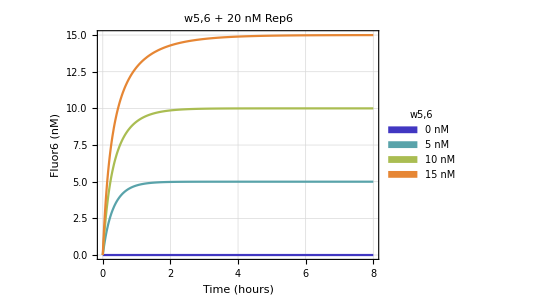

```mathematica
concRep=20;
concW={0,5,10,15};
krep=5*10^4;
SIMtime=8; 
trajectories={"0 nM", "5 nM", "10 nM", "15 nM"};
TrajectoryLabel="w5,6";
OutputLabel="Fluor6 (nM)";
CircuitLabel="w5,6 + 20 nM Rep6";  
PlotSim[SIMcircuit[concRep,concW,krep,SIMtime],
SIMtime,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

## Data analysis (data1)

### Import data from a .csv file

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Lab03_data1.csv"];
```

### Plot raw data

Use DataToList defined in Functions to convert the imported data to a list in the format of {time, raw fluorescence}:

Revise the delay time to 5 minutes, which was recorded from the experiment.

```mathematica
delay = 5/60;   (* delay time between the sample was mixed and the measurement was started, unit: hours *)
datalist=DataToList[data,delay];
```

Use PlotData defined in Functions to generate a plot of a datalist:

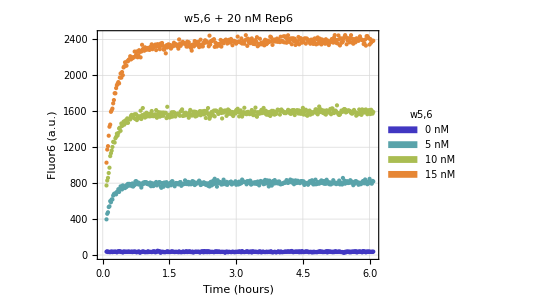

```mathematica
trajectories={"0 nM", "5 nM", "10 nM", "15 nM"};
TrajectoryLabel="w5,6";
OutputLabel="Fluor6 (a.u.)"; (* the unit for raw data is arbitrary fluorescence level (a.u.) *)
CircuitLabel="w5,6 + 20 nM Rep6";  
PlotData[datalist,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

### Plot normalized data

Use NormalizeDataList defined in Functions to convert/normalize raw fluorescence data to concentration data:
two reference points are given here: 
average of the first 5 data points of the 1st trajectory (i.e. w5,6 = 0 nM) is 0 nM
average of the last 5 data points of the 4th trajectory (i.e. w5,6 = 15 nM) is 15 nM

Revise the reference list to include two more reference points: the average of the last 5 data points of the 2nd trajectory should be 5 nM, and the average of the last 5 data points of the 3rd trajectory should be 10 nM.

```mathematica
referencelist={{1,0,0},{2,1,5},{3,1,10},{4,1,15}};
datalistNorm=NormalizeDataList[datalist,referencelist];
```

Use PlotData defined in Functions to generate a plot of a normalized datalist:

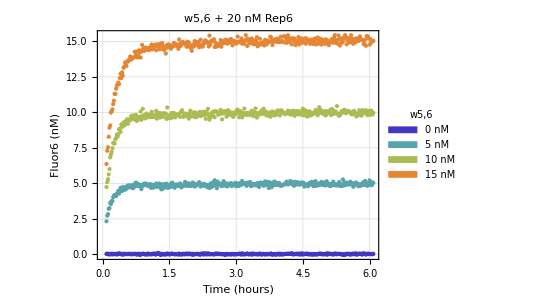

```mathematica
trajectories={"0 nM", "5 nM", "10 nM", "15 nM"};
TrajectoryLabel="w5,6";
OutputLabel="Fluor6 (nM)";
CircuitLabel="w5,6 + 20 nM Rep6";  
PlotData[datalistNorm,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

### Plot normalized data overlaid with simulation

Use built-in function Manipulate to tune target parameters, krep in this example:
Note: Manipulate dynamically updates based on all definitions in the same kernel. We can use built-in function With for use-once local definitions here so that the plot will not be updated because of later uses of the same variable names.

Revise the definitions to include the changes that you have made in the simulation above, and revise the time range to display just the part of the trajectories that are relevant for finding a reaction rate constant.

Does the simulation agree with the experimental data? If not, find a rate constant krep that fits the data reasonably well.

```mathematica
With[{concRep=20,
concW={0,5,10,15},
SIMtime=8,
trajectories={"0 nM", "5 nM", "10 nM", "15 nM"},
TrajectoryLabel="w5,6",
OutputLabel="Fluor6 (nM)",
CircuitLabel="w5,6 + 20 nM Rep6",  
TimeRange={0,2}},
Manipulate[Show[{PlotSim[SIMcircuit[concRep,concW,krep,SIMtime],
SIMtime,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel,TimeRange],
PlotData[datalistNorm]}],
{{krep,11.6*10^4},10^3,10^6}]]
```

### Export normalized data overlaid with simulation

Apply the same changes to the following definitions and export a plot of normalized data overlaid with simulation, specifying the krep that you found.

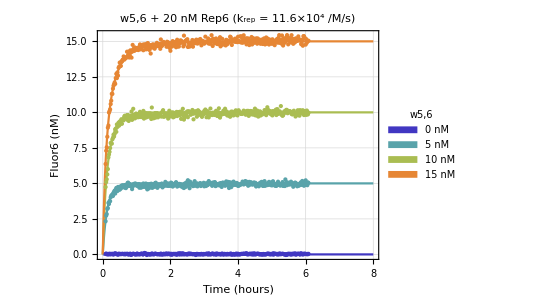

```mathematica
concRep=20;
concW={0,5,10,15};
krep=11.6*10^4;
SIMtime=8;
trajectories={"0 nM", "5 nM", "10 nM", "15 nM"};
TrajectoryLabel="w5,6";
OutputLabel="Fluor6 (nM)";
CircuitLabel="w5,6 + 20 nM Rep6\n (k_rep = 11.6×10^4 /M/s)";  
TimeRange=All;
Lab03SimData1=Show[{PlotSim[SIMcircuit[concRep,concW,krep,SIMtime],
SIMtime,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel,TimeRange],
PlotData[datalistNorm]}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
data=Export["Lab03SimData1.png",Lab03SimData1,ImageResolution->300,Background->None];
```